```mathematica
a[n_]=(1+ 1/n)^n
```

(1+1/n)^n

```mathematica
a[1]
```

2

```mathematica
a[10]
```

25937424601/10000000000

```mathematica
N[%]
```

2.59374

```mathematica
N[a[1000]]
```

2.71692

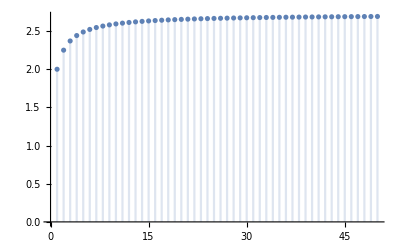

```mathematica
DiscretePlot[a[n],{n,1,50}]
```

```mathematica
Limit[a[n], n->Infinity]
```

ⅇ

```mathematica
N[%,10]
```

```mathematica
2.71828182845904523537395799936966511723`10.
N[a[10],10]
```

2.718281828

2.59374246

```mathematica
N[a[100],10]
```

2.704813829

```mathematica
N[a[1000],10]
```

2.716923932

```mathematica
b[n_]=∑_(k=0)^n 1/k!
```

(ⅇ Gamma[1+n,1])/Gamma[1+n]

```mathematica
Limit[b[n],n->Infinity]
```

```mathematica
ⅇ
N[b[10],10]
```

ⅇ

2.718281801

```mathematica
N[E,25]
```

2.718281828459045235360287

```mathematica
N[b[20],25]
```

2.718281828459045235339784

Exercisi 2

```mathematica
s[n_]=((2n + 1)/(2n -√n))^√(n+2)
```

((1+2 n)/(-√n+2 n))^(√(2+n))

```mathematica
Limit [s[n],n->Infinity]
```

√ⅇ

Exercisi 3

```mathematica
(n+1)^3
```

(1+n)^3

```mathematica
Limit[(∑_(k=1)^n k^2)/n^3, n-> Infinity]
```

1/3

Exercisi 4

```mathematica
a[n_]=√(n^5)-√(n^3+1)
```

√(n^5)-√(1+n^3)

```mathematica
b[n_]=Log[n]
```

Log[n]

```mathematica
Limit[a[n]/b[n], n -> Infinity]
```

∞

Exercisi 5: Totes tendeixen a infinit

```mathematica
Limit[n,n->Infinity]
```

∞

```mathematica
Limit[Log[n],n->Infinity]
```

∞

Ara cal comparar dos a dos totes les expressions:

```mathematica
Limit[n/n^2, n -> Infinity]
```

0

```mathematica
Limit[n^2/√(n^3),n  -> Infinity]
```

∞

```mathematica
Limit[n/Log[n],  n-> Infinity]
```

```mathematica
∞
```

```mathematica
Limit[√(n^3)/n,  n-> Infinity]
```

∞

Exercisi 6

```mathematica
z[n_]=√(n^5+2)-√(n^4-1)
```

-√(-1+n^4)+√(2+n^5)

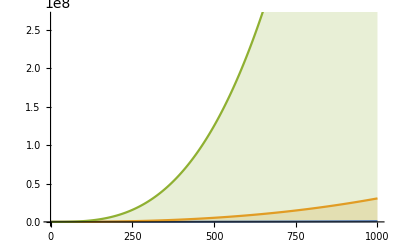

```mathematica
DiscretePlot[{n^2,z[n],n^(2+1)},{n,1,1000}]
```